Assignment 3
Group 4
Jordan Earle - 12297127
Martin Frassek - 12236632

Exercise 1

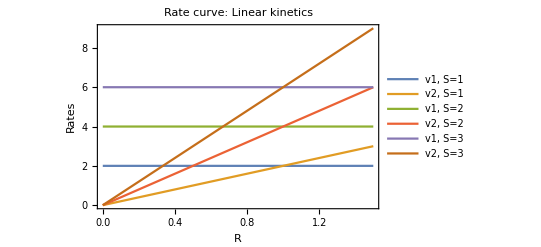

```mathematica
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};
x = k3*s/k4;
ratesa = {v1 -> k1*s, v2 -> k2*x*r};

Plot[{
v1/.ratesa/.rateconsta/.s->1,
v2/.ratesa/.rateconsta/.s->1,
v1/.ratesa/.rateconsta/.s->2,
v2/.ratesa/.rateconsta/.s->2,
v1/.ratesa/.rateconsta/.s->3,
v2/.ratesa/.rateconsta/.s->3},

{r,0,1.5},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v2, S=1", "v1, S=2", "v2, S=2", "v1, S=3", "v2, S=3"}, 
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18] ]
```

You can plot it and it would show  a constant response independent of the signal, which will be approximately 1.

Storing some shit since I cant figure it out

Solve[dR == 0, dX == 0, {r[t], x[t]}]

Plot[x[t]=Floor[t/4],{t,0,20}]
Plot[r[t],{t,0,20}]
ListStepPlot[{{0,0},{4,1},{8,2},{12,3},{16,4}}]

Floor[t/4]

r'==2 s-2 r x

x'==s-x

{{x[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

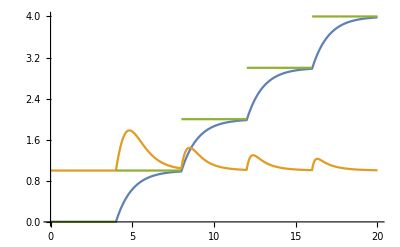

```mathematica
ClearAll["Global`*"];

ratesa = {v1 -> k1*s, v2 -> k2*x*r, v3 -> k3*s, v4 -> k4*x};
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};

s[t_] = Floor[t/4]

eqr = r' == (k1*s) - (k2*x*r)/.ratesa/.rateconsta
eqx = x' == (k3*s) - (k4*x)/.ratesa/.rateconsta

solx = NDSolve[Evaluate[{x'[t] == (1*s[t]) - (1*x[t]), r'[t] == (2*s[t]) - (2*x[t]*r[t]),r[0] == 1,x[0] == 0}], {x[t], r[t]}, {t, 0, 20}]
Plot[{x[t]/.solx, r[t]/.solx, s[t]}, {t,0,20}]
```